```mathematica
Clear["Global`*"]
```

## Coherent States - Zero Mean, Large Deviation

### A priori probability P(α)

```mathematica
PαEven[α_,σ_]:=1/(5σ α);
Pα[α_,σ_]:=2./(√(2.π)σ α)Exp[-α^2/(2. σ^2)];
αmin=0;
αmax[σ_]:=5.σ;
nmax[σ_]:=25.(σ^2+σ);
```

### The transfer probabilities

```mathematica
pnea[NN_,Ne_,α_,φ_,σ_]:=Re[Sum[
Exp[-α^2.] α^(2.n)/(n!)(NN!)/((NN-Ne)!Ne!)Sin[n φ/2.]^(2.Ne)Cos[n φ/2.]^(2.(NN-Ne)),
{n,0,nmax[σ]}]]/;Ne≠0;
pnea[NN_,Ne_,α_,φ_,σ_]:=Re[Sum[
Exp[-α^2] α^(2.n)/(n!)Cos[n φ/2.]^(2.NN),
{n,0,nmax[σ]}]]/;Ne==0;
```

### The total probability for Ne

```mathematica
pne[NN_,Ne_,φ_,σ_]:=Re[NIntegrate[Pα[α,σ]α pnea[NN,Ne,α,φ,σ],{α,0,αmax[σ]}]];
```

### The conditional probability

```mathematica
pane[NN_,Ne_,α_,φ_,σ_]:=pnea[NN,Ne,α,φ,σ] Pα[α,σ]/pne[NN,Ne,φ,σ];
```

#### Test:

```mathematica
αmin=0.0001
```

0.0001

```mathematica
datapane80=ParallelTable[{α,pane[8,0,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane81=ParallelTable[{α,pane[8,1,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane82=ParallelTable[{α,pane[8,2,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane83=ParallelTable[{α,pane[8,3,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane84=ParallelTable[{α,pane[8,4,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane85=ParallelTable[{α,pane[8,5,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane86=ParallelTable[{α,pane[8,6,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane87=ParallelTable[{α,pane[8,7,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
datapane88=ParallelTable[{α,pane[8,8,α,0.3523,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
```

```mathematica
datapane8=SetAccuracy[Re[Table[{αmin+0.02*(n-1),
datapane80[[n]][[2]],
datapane81[[n]][[2]],
datapane82[[n]][[2]],
datapane83[[n]][[2]],
datapane84[[n]][[2]],
datapane85[[n]][[2]],
datapane86[[n]][[2]],
datapane87[[n]][[2]],
datapane88[[n]][[2]]},
{n,304}]],6];
```

```mathematica
Export["datapane8.dat",datapane8,"Table"]
```

datapane8.dat

```mathematica
datapne8=ParallelTable[{Ne,pne[8,Ne,0.3523,√2.]},{Ne,0,8,1}]
```

{{0,0.637229},{1,0.102665},{2,0.0595255},{3,0.0420439},{4,0.0331159},{5,0.0282361},{6,0.0261037},{7,0.0273848},{8,0.0436958+0. ⅈ}}

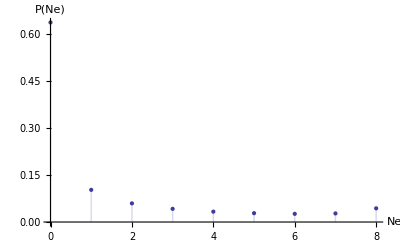

```mathematica
ListPlot[datapne8,PlotRange->Full,PlotStyle->{Dot},AxesStyle->Larger,AxesLabel->{"Ne","P(Ne)"},Filling->Axis]
```

```mathematica
datapa=Table[{α,Pα[α,√2.]α},{α,αmin,αmax[√2.]-1,0.02}];
```

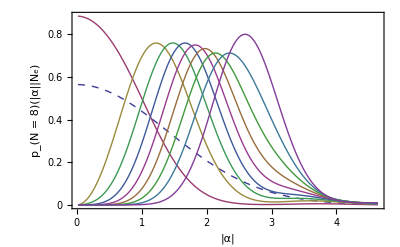

```mathematica
ListLinePlot[{datapa,datapane80,datapane81,datapane82,datapane83,datapane84,datapane85,datapane86,datapane87,datapane88},Frame->True,FrameStyle->Larger,FrameTicks->{{0,1,2,3,4},{0,0.2,0.4,0.6,0.8}},FrameLabel->{{"p_(N = 8)(|α||N_e)"},{"|α|"}},PlotStyle->{{Thick,Dashed},{},{},{},{},{},{},{},{},{}},PlotRange->
Full]
```

### Information Gain: 1 - F

#### The initial info gain:1 - F

```mathematica
IFi[σ_]:=1-NIntegrate[PαEven[α,σ]^(1/2)Pα[α,σ]^(1/2)α,{α,0,αmax[σ]}]^2;
```

```mathematica
IFNe[NN_,Ne_,φ_,σ_]:=Re[NIntegrate[PαEven[α,σ]^(1/2)pane[NN,Ne,α,φ,σ]^(1/2)α,{α,0,αmax[σ]}]]^2;
IF[NN_,φ_,σ_]:=1-Sum[IFNe[NN,Ne,φ,σ]pne[NN,Ne,φ,σ],{Ne,0,NN}]-IFi[σ];
```

### Information Gain: Mutual Information

```mathematica
HH[NN_,Ne_,φ_,σ_]:=Re[NIntegrate[Pα[α,σ]α pnea[NN,Ne,α,φ,σ]Log[2,pnea[NN,Ne,α,φ,σ]],{α,0,αmax[σ]}]];
INC[NN_,φ_,σ_]:=Re[Sum[HH[NN,Ne,φ,σ]-pne[NN,Ne,φ,σ]Log[2,pne[NN,Ne,φ,σ]],{Ne,0,NN}]];
```

### Fidelity - Single Measurement

```mathematica
Fαφ[α_,φ_,σ_]:=(Abs[Sum[Exp[-α^2] α^(2.n)/(n!)Sin[n φ/2]Exp[-I n φ/2],{n,1,nmax[σ]}]])^2+(Abs[Exp[-α^2]+Sum[Exp[-α^2] α^(2.n)/(n!)Cos[n φ/2]Exp[-I n φ/2],{n,1,nmax[σ]}]])^2;
Fφ[φ_,σ_]:=Re[NIntegrate[Fαφ[α,φ,σ]Pα[α,σ]α,{α,0,αmax[σ]}]];
```

### Fidelity - Measuring N times

```mathematica
FαϕN[α_,φ_,NN_,σ_]:=Sum[(Abs[Sum[Exp[-α^2] α^(2.n)/(n!)Sin[n φ/2]^Ne Cos[n φ/2]^(NN-Ne)Exp[-I n NN φ/2],{n,1,nmax[σ]}]])^2,{Ne,1,NN}]+(Abs[Exp[-α^2]+Sum[Exp[-α^2] α^(2.n)/(n!)Cos[n φ/2]^NN Exp[-I NN n φ/2],{n,1,nmax[σ]}]])^2;
FφN[φ_,NN_,σ_]:=Re[NIntegrate[FαϕN[α,φ,NN,σ]Pα[α,σ]α,{α,0,αmax[σ]}]];
```

## Data and Plot:

### Single Measurement

#### σ^2=2, Information gain and fidelity vs φ

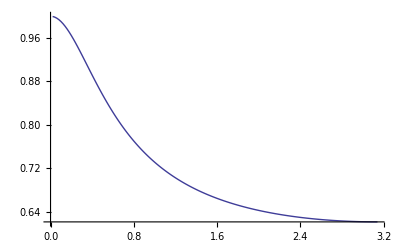

```mathematica
ListLinePlot[ParallelTable[{φ,Fφ[φ,√2]},{φ,0.02, 3.14, 0.02}]]
```

```mathematica
NNlist=Join[{1,2},Round[Table[2^(x/4),{x,7,40}]]]
```

{1,2,3,4,5,6,7,8,10,11,13,16,19,23,27,32,38,45,54,64,76,91,108,128,152,181,215,256,304,362,431,512,609,724,861,1024}

```mathematica
Length[NNlist]
```

36

```mathematica
dataIF=ParallelTable[{NN,IF[NN,π/32.,√2.]},{NN,NNlist}];
```

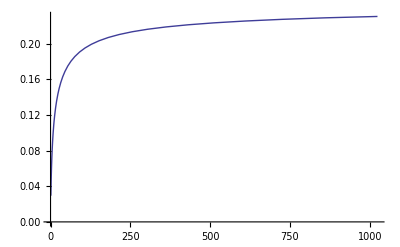

```mathematica
ListLinePlot[dataIF]
```

### Export “CS_IF_NN.dat”

```mathematica
Export["CS_IF_NN_2.dat",dataIF,"Table"]
```

CS_IF2_NN.dat

```mathematica
dataIF05=ParallelTable[{φ,IF[1,φ,√0.5]},{φ,0.02,3.14,0.02}];
dataIF1=ParallelTable[{φ,IF[1,φ,1.]},{φ,0.02,3.14,0.02}];
dataIF2=ParallelTable[{φ,IF[1,φ,√2.]},{φ,0.02,3.14,0.02}];
dataIF4=ParallelTable[{φ,IF[1,φ,2]},{φ,0.02,3.14,0.02}];
dataIF8=ParallelTable[{φ,IF[1,φ,√8.]},{φ,0.02,3.14,0.02}];
```

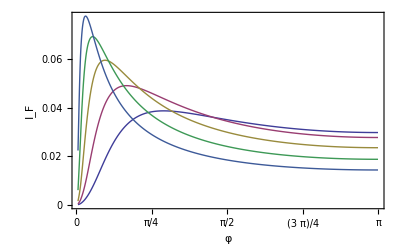

```mathematica
ListLinePlot[{dataIF05,dataIF1,dataIF2,dataIF4,dataIF8},InterpolationOrder->2,Frame->True,FrameStyle->Larger,PlotRange->Full,FrameTicks->{{0,π/4,π/2,3π/4,π},{0,0.02,0.04,0.06}},FrameLabel->{"φ","I_F"},RotateLabel->False]
```

```mathematica
dataIFN=SetAccuracy[Re[Table[{n*0.02,
dataIF05[[n]][[2]],
dataIF1[[n]][[2]],
dataIF2[[n]][[2]],
dataIF4[[n]][[2]],
dataIF8[[n]][[2]]},
{n,1,157}]],6];
```

### Export “CS_IF_N1.dat”

```mathematica
Export["CS_IF_N1_2.dat",dataIFN,"Table"]
```

CS_IF2_N1.dat

```mathematica
dataIFφ1=ParallelTable[{φ,IF[1,φ,√2.]},{φ,0.02,3.14,0.02}];
dataIFφ2=ParallelTable[{φ,IF[2,φ,√2.]},{φ,0.02,3.14,0.02}];
dataIFφ4=ParallelTable[{φ,IF[4,φ,√2.]},{φ,0.02,3.14,0.02}];
dataIFφ8=ParallelTable[{φ,IF[8,φ,√2.]},{φ,0.02,3.14,0.02}];
dataIFφ16=ParallelTable[{φ,IF[16,φ,√2.]},{φ,0.02,3.14,0.02}];
```

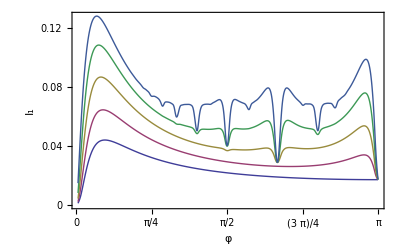

```mathematica
pIFφ=ListLinePlot[{dataIFφ1,dataIFφ2,dataIFφ4,dataIFφ8,dataIFφ16},PlotRange->Full,InterpolationOrder->3,Frame->True,FrameStyle->Larger,PlotRange->Full,FrameTicks->{{0,π/4,π/2,3π/4,π},{0,0.04,0.08,0.12}},FrameLabel->{"φ","I_1"},RotateLabel->False,ImagePadding->50]
```

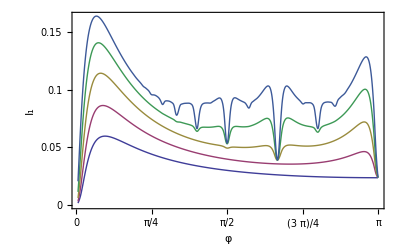

```mathematica
pIFφ=ListLinePlot[{dataIFφ1,dataIFφ2,dataIFφ4,dataIFφ8,dataIFφ16},PlotRange->Full,InterpolationOrder->3,Frame->True,FrameStyle->Larger,PlotRange->Full,FrameTicks->{{0,π/4,π/2,3π/4,π},{0,0.05,0.10,0.15}},FrameLabel->{"φ","I_1"},RotateLabel->False,ImagePadding->50]
```

```mathematica
dataIFphi=SetAccuracy[Re[Table[{n*0.02,
dataIFφ1[[n]][[2]],
dataIFφ2[[n]][[2]],
dataIFφ4[[n]][[2]],
dataIFφ8[[n]][[2]],
dataIFφ16[[n]][[2]]},
{n,1,157}]],6];
```

### Export “CS_IF_phi.dat”

```mathematica
Export["CS_IF2_phi.dat",dataIFphi,"Table"]
```

CS_IF2_phi.dat

#### Test

```mathematica
dataIN05=ParallelTable[{φ,INC[1,φ,√0.5]},{φ,0.02,3.14,0.02}];
dataIN1=ParallelTable[{φ,INC[1,φ,1.]},{φ,0.02,3.14,0.02}];
dataIN2=ParallelTable[{φ,INC[1,φ,√2.]},{φ,0.02,3.14,0.02}];
dataIN4=ParallelTable[{φ,INC[1,φ,2]},{φ,0.02,3.14,0.02}];
dataIN8=ParallelTable[{φ,INC[1,φ,√8.]},{φ,0.02,3.14,0.02}];
```

```mathematica
dataIN=SetAccuracy[Re[Table[{n*0.02,
dataIN05[[n]][[2]],
dataIN1[[n]][[2]],
dataIN17[[n]][[2]],
dataIN2[[n]][[2]],
dataIN34[[n]][[2]]},
{n,1,157}]],6];
```

### Export “CS_IM_N1.dat”

```mathematica
Export["dataIN.dat",dataIN,"Table"]
```

dataIN.dat

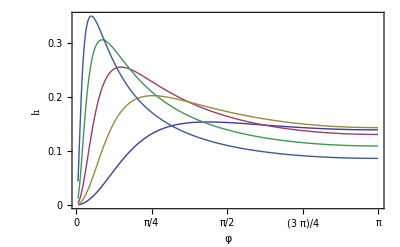

```mathematica
pI1=ListLinePlot[{dataIN05,dataIN17,dataIN1,dataIN2,dataIN34},InterpolationOrder->2,Frame->True,FrameStyle->Larger,PlotRange->Full,FrameTicks->{{0,π/4,π/2,3π/4,π},{0,0.1,0.2,0.3}},FrameLabel->{"φ","I_1"},RotateLabel->False]
```

```mathematica
Timing[INC[1,π/32,√2]]
```

{0.0624,0.0629385}

```mathematica
dataIM=ParallelTable[{NN,INC[NN,π/32.,√2.]},{NN,NNlist}];
```

### Export “CS_IM_NN.dat”

```mathematica
Export["CS_IM_NN.dat",dataIM,"Table"]
```

CS_IM_NN.dat

```mathematica
dataINφ1=ParallelTable[{φ,INC[1,φ,√2.]},{φ,0.02,3.14,0.02}];
dataINφ2=ParallelTable[{φ,INC[2,φ,√2.]},{φ,0.02,3.14,0.02}];
dataINφ4=ParallelTable[{φ,INC[4,φ,√2.]},{φ,0.02,3.14,0.02}];
dataINφ8=ParallelTable[{φ,INC[8,φ,√2.]},{φ,0.02,3.14,0.02}];
dataINφ16=ParallelTable[{φ,INC[16,φ,√2.]},{φ,0.02,3.14,0.02}];
```

```mathematica
dataIMphi=SetAccuracy[Re[Table[{n*0.02,
dataINφ1[[n]][[2]],
dataINφ2[[n]][[2]],
dataINφ4[[n]][[2]],
dataINφ8[[n]][[2]],
dataINφ16[[n]][[2]]},
{n,1,157}]],6];
```

### Export “CS_IM_phi.dat”

```mathematica
Export["CS_IM_phi.dat",dataIMphi,"Table"]
```

CS_IM_phi.dat

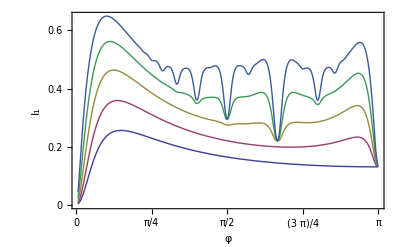

```mathematica
pINφ=ListLinePlot[{dataINφ1,dataINφ2,dataINφ4,dataINφ8,dataINφ16},PlotRange->Full,InterpolationOrder->3,Frame->True,FrameStyle->Larger,PlotRange->Full,FrameTicks->{{0,π/4,π/2,3π/4,π},{0,0.2,0.4,0.6}},FrameLabel->{"φ","I_1"},RotateLabel->False,ImagePadding->50]
```

### Export “CS_I-F_N1”

```mathematica
dataIF2=ParallelTable[{φ,IF[1,φ,√2.]},{φ,0.02,3.14,0.02}];
```

```mathematica
dataIN2=ParallelTable[{φ,INC[1,φ,√2.]},{φ,0.02,3.14,0.02}];
```

```mathematica
dataF2=ParallelTable[{φ,Fφ[φ,√2.]},{φ,0.02,3.14,0.02}];
```

```mathematica
dataIFN1=SetAccuracy[Re[Table[{n*0.02,
dataIN2[[n]][[2]],
dataIF2[[n]][[2]],
dataF2[[n]][[2]]},
{n,1,157}]],6];
```

```mathematica
Export["CS_I-F_N1_2.dat",dataIFN1,"Table"]
```

CS_I-F_N1_2.dat